```mathematica
Clear oscillation;
oscillation[T_,U_,q_,t_]:=With[{M=Normal[Last[CoefficientArrays[T,D[q,t],"Symmetric"->True]]],K=Normal[Last[CoefficientArrays[U,q,"Symmetric"->True]]]},With[{ws=Table[w/.Solve[Det[-M w+K]==0,w][[i]],{i,1,Length[q]}]},Table[{ws[[i]],NullSpace[(-M ws[[i]]+K)]},{i,1,Length[q]}]]];
T = (m q1'[t]^2)/2+(m q2'[t]^2)/2;
U = (k(q2[t] - q1[t])^2)/2;
oscillation[T,U,{q1[t],q2[t]},t]
```

{{0,{{1,1}}},{(2 k)/m,{{-1,1}}}}

```mathematica
T = (m1 q1'[t]^2)/2+(m2 q2'[t]^2)/2;
U = (k(q2[t] - q1[t])^2)/2;
oscillation[T,U,{q1[t],q2[t]},t]
```

{{0,{{1,1}}},{(k (m1+m2))/(m1 m2),{{-m2/m1,1}}}}

```mathematica
T = (m1 q1'[t]^2)/2+(m1 q2'[t]^2)/2+(m2 q3'[t]^2)/2;
U = (k(q2[t] - q1[t])^2)/2+(k(q3[t] - q2[t])^2)/2+(k(q1[t] - q3[t])^2)/2;
oscillation[T,U,{q1[t],q2[t],q3[t]},t]
```

{{0,{{1,1,1}}},{(3 k)/m1,{{-1,1,0}}},{(k (2 m1+m2))/(m1 m2),{{-m2/(2 m1),-m2/(2 m1),1}}}}

```mathematica
T = ((m1+m2)L1^2 q1'[t]^2)/2+(m2 L2^2 q2'[t]^2)/2+ m2 L1 L2 q2'[t]q1'[t];
U = ((m1+m2) g L1 (q1[t])^2)/2+(m2 g L2(q2[t])^2)/2;
sol = oscillation[T,U,{q1[t],q2[t]},t]
```

{{(g L1 m1+g L2 m1+g L1 m2+g L2 m2-g √(m1+m2) √(L1^2 m1-2 L1 L2 m1+L2^2 m1+L1^2 m2+2 L1 L2 m2+L2^2 m2))/(2 L1 L2 m1),{{(m2 (g L1 m1+g L2 m1+g L1 m2+g L2 m2-g √(m1+m2) √(L1^2 m1-2 L1 L2 m1+L2^2 m1+L1^2 m2+2 L1 L2 m2+L2^2 m2)))/(4 m1 (1/2 g L1 (m1+m2)-(L1 (m1+m2) (g L1 m1+g L2 m1+g L1 m2+g L2 m2-g √(m1+m2) √(L1^2 m1-2 L1 L2 m1+L2^2 m1+L1^2 m2+2 L1 L2 m2+L2^2 m2)))/(4 L2 m1))),1}}},{(g L1 m1+g L2 m1+g L1 m2+g L2 m2+g √(m1+m2) √(L1^2 m1-2 L1 L2 m1+L2^2 m1+L1^2 m2+2 L1 L2 m2+L2^2 m2))/(2 L1 L2 m1),{{(m2 (g L1 m1+g L2 m1+g L1 m2+g L2 m2+g √(m1+m2) √(L1^2 m1-2 L1 L2 m1+L2^2 m1+L1^2 m2+2 L1 L2 m2+L2^2 m2)))/(4 m1 (1/2 g L1 (m1+m2)-(L1 (m1+m2) (g L1 m1+g L2 m1+g L1 m2+g L2 m2+g √(m1+m2) √(L1^2 m1-2 L1 L2 m1+L2^2 m1+L1^2 m2+2 L1 L2 m2+L2^2 m2)))/(4 L2 m1))),1}}}}

```mathematica
q=Sum[C0[i]Flatten[Last[sol[[i]]]]Cos[First[sol[[i]]]t+ϕ0[i]],{i,1,2}];
move=(q/.{ϕ0[i_]->2/10,C0[i_]->3/10})/.{g->1/10,m1->1/10,m2->2/10,L1->1,L2->1/2};
```

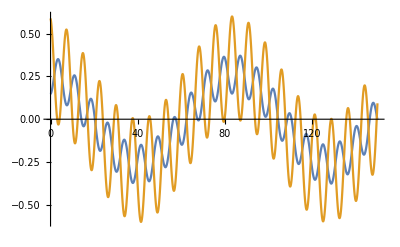

```mathematica
Plot[move,{t,0,150}]
```

```mathematica
Animate[ListPlot[{{0,0},{-1Sin[move[[1]]]/.{t->t1},-1Cos[move[[1]]]/.{t->t1}},{-1Sin[move[[1]]]-1/2Sin[move[[2]]]/.{t->t1},-1Cos[move[[1]]]-1/2Cos[move[[2]]]/.{t->t1}}},AspectRatio->1,PlotRange->{{-2,2},{-2,0}},PlotStyle->Directive[Red,PointSize[0.04]],Joined->True,PlotMarkers->{Automatic,12}],{t1,0,82}] 
(*рисую координаты х и у каждого груза: -Li*sin(phi) -Li*cos(phi)*)
```